# Pd DCA vary T

## tpd=1.13,tpp=0.49,Udd=8.5,Upp=0

## beta=16, L=2*2

```mathematica
dcan2by2b16Upp0={0.7,0.75,0.8,0.85,0.9,0.95,1,1.05,1.1 ,1.15,1.2,1.25,1.3};
```

```mathematica
dcapdtot2by2b16Upp0={11.086995794131523,11.3205603781363,11.420232461449709,11.258290585735915,10.70995598154093,9.621493154733887,6.277473426278576,7.973150180508461,8.21766441434449,8.274763986388505,8.157116699675043,8.009842267608606,7.7821679306436655};
```

```mathematica
dcald2by2b16Upp0={0.232361672,0.311363046,0.403904857,0.506273943,0.615594955,0.727628996,0.907736914,0.767524438,0.623983068,0.492433379,0.357293785,0.232667083,0.119945471};
```

```mathematica
Pd0b16={5.659296157454506,5.224737697906308,4.616725761223142,3.8190692114480975,2.8540624296061874,1.7770549774924742,0.2794768985833898,1.0936274045324919,1.8387567398002045,2.4861977654056115,3.036965343760427,3.518711199058158,3.8244153362713584};
```

```mathematica
dcaldpd2by2b16Upp0=Table[1/(1-dcald2by2b16Upp0[[i]]),{i,1,Length[dcald2by2b16Upp0]}];
```

```mathematica
dcapd0tot2by2b16Upp0=Table[dcapdtot2by2b16Upp0[[i]]/dcaldpd2by2b16Upp0[[i]],{i,1,Length[dcald2by2b16Upp0]}];
```

```mathematica
dcapdseptot2by2b16Upp0=Table[Pd0b16[[i]]/(1-dcald2by2b16Upp0[[i]]),{i,1,Length[dcald2by2b16Upp0]}];
```

```mathematica
dcapdseptotvsn2by2b16Upp0=Table[{dcan2by2b16Upp0[[i]],dcapdseptot2by2b16Upp0[[i]]},{i,1,13}];
```

```mathematica
dcapdtotvsn2by2b16Upp0=Table[{dcan2by2b16Upp0[[i]],dcapdtot2by2b16Upp0[[i]]},{i,1,13}];
```

```mathematica
dcaldvsn2by2b16Upp0=Table[{dcan2by2b16Upp0[[i]],dcald2by2b16Upp0[[i]]},{i,1,13}];
```

```mathematica
dcaldpdvsn2by2b16Upp0=Table[{dcan2by2b16Upp0[[i]],dcaldpd2by2b16Upp0[[i]]},{i,1,13}];
```

```mathematica
dcapd0totvsn2by2b16Upp0=Table[{dcan2by2b16Upp0[[i]],dcapd0tot2by2b16Upp0[[i]]},{i,1,13}];
```

```mathematica
Pd0b16vsdensity=Table[{dcan2by2b16Upp0[[i]],Pd0b16[[i]]},{i,1,13}];
```

## beta=32, L=2*2

```mathematica
dcan2by2b32Upp0={0.7,0.75,0.8,0.85,0.9,0.95,1,1.05,1.1 ,1.15,1.2,1.25,1.3};
```

```mathematica
dcapdtot2by2b32Upp0={14.500978872452166,16.23316637091925,19.22757580429356,23.857881756677862,30.978313833252837,42.62273134599052,6.469745452591532,40.175716428441746,23.617436836260417,16.282097805765826,13.066926595951957,11.09250612915983,10.164235984888219};
```

```mathematica
dcald2by2b32Upp0={0.340374365,0.47586109,0.641879513,0.792474713,0.906618415,0.959055003,0.972321082516868,0.975730012,0.919344176,0.801953254,0.632283593,0.431208798,0.251127268};
```

```mathematica
Pd0b32={6.9028911320611455,6.388463588130897,5.466314202844943,4.153169178051157,2.6786985279027262,1.45688006840169,0.07977324488441197,0.8501589882348755,1.5995341704774162,2.5356876056024715,3.461825407203943,4.296517779024532,4.8187892612976455};
```

```mathematica
dcaldpd2by2b32Upp0=Table[1/(1-dcald2by2b32Upp0[[i]]),{i,1,Length[dcald2by2b16Upp0]}];
```

```mathematica
dcapd0tot2by2b32Upp0=Table[dcapdtot2by2b32Upp0[[i]]/dcaldpd2by2b32Upp0[[i]],{i,1,Length[dcald2by2b32Upp0]}];
```

```mathematica
dcapdseptot2by2b32Upp0=Table[Pd0b32[[i]]/(1-dcald2by2b32Upp0[[i]]),{i,1,Length[dcald2by2b32Upp0]}];
```

```mathematica
dcapdseptotvsn2by2b32Upp0=Table[{dcan2by2b32Upp0[[i]],dcapdseptot2by2b32Upp0[[i]]},{i,1,13}];
```

```mathematica
dcapdtotvsn2by2b32Upp0=Table[{dcan2by2b32Upp0[[i]],dcapdtot2by2b32Upp0[[i]]},{i,1,13}];
```

```mathematica
dcaldvsn2by2b32Upp0=Table[{dcan2by2b32Upp0[[i]],dcald2by2b32Upp0[[i]]},{i,1,13}];
```

```mathematica
dcaldpdvsn2by2b32Upp0=Table[{dcan2by2b32Upp0[[i]],dcaldpd2by2b32Upp0[[i]]},{i,1,13}];
```

```mathematica
dcapd0totvsn2by2b32Upp0=Table[{dcan2by2b32Upp0[[i]],dcapd0tot2by2b32Upp0[[i]]},{i,1,13}];
```

```mathematica
Pd0b32vsdensity=Table[{dcan2by2b32Upp0[[i]],Pd0b32[[i]]},{i,1,13}];
```

```mathematica
ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

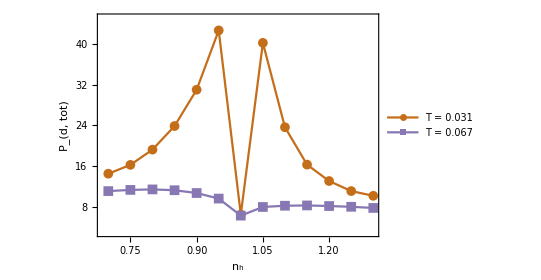

```mathematica
dcapdtotvsn2by2Upp0varyT=ListPlot[{dcapdtotvsn2by2b32Upp0,dcapdtotvsn2by2b16Upp0},PlotMarkers->{Automatic,10},PlotRange->{Automatic,{3,45}},PlotStyle->{RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.528488, 0.470624, 0.701351]},PlotLegends->Placed[LineLegend[{"T = 0.031","T = 0.067"},LabelStyle->{14},LegendLayout->{"Row",2}],{0.18,0.82}],Frame->True,AspectRatio->0.7,BaseStyle->{FontSize->18,FontFamily->"times New Roman"},FrameLabel->{"n_h","P_(d, tot)","L=2*2"},Joined->True]
```

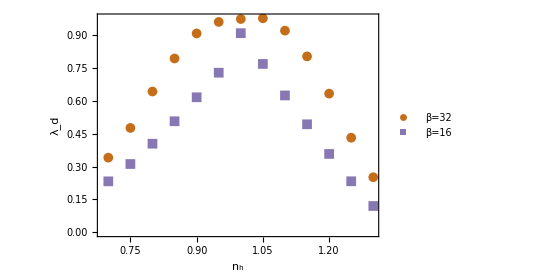

```mathematica
dcaldvsn2by2Upp0varyT=ListPlot[{dcaldvsn2by2b32Upp0,dcaldvsn2by2b16Upp0},PlotMarkers->{Automatic,10},PlotLegends->Placed[LineLegend[{"β=32","β=16"},LabelStyle->{14},LegendLayout->{"Row",2}],{0.5,0.2}],Frame->True,AspectRatio->0.7,BaseStyle->{FontSize->18,FontFamily->"times New Roman"},PlotStyle->{RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.528488, 0.470624, 0.701351]},FrameLabel->{"n_h","λ_d","L=2*2"}]
```

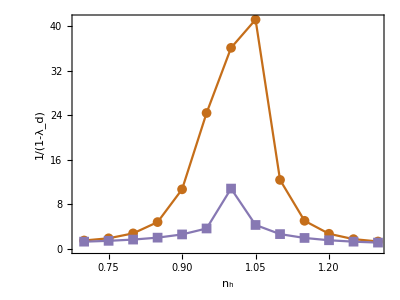

```mathematica
dcaldpdvsn2by2Upp0varyT=ListPlot[{dcaldpdvsn2by2b32Upp0,dcaldpdvsn2by2b16Upp0},PlotMarkers->{Automatic,10},PlotStyle->{RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.528488, 0.470624, 0.701351]},(*PlotLegends->Placed[LineLegend[{"β=32","β=16"},LabelStyle->{14},LegendLayout->{"Row",2}],{0.2,0.8}],*)Frame->True,AspectRatio->0.75,BaseStyle->{FontSize->18,FontFamily->"times New Roman"},FrameLabel->{"n_h","1/(1-λ_d)","L=4*4"},PlotRange->All,Joined->True]
```

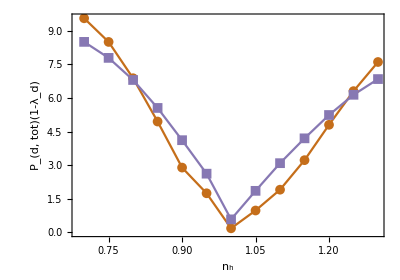

```mathematica
dcapd0totvsn2by2Upp0varyT=ListPlot[{dcapd0totvsn2by2b32Upp0,dcapd0totvsn2by2b16Upp0},PlotMarkers->{Automatic,10},PlotStyle->{RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.528488, 0.470624, 0.701351]},(*PlotLegends->Placed[LineLegend[{"β=32","β=16"},LabelStyle->{14},LegendLayout->{"Row",2}],{0.15,0.2}],*)Frame->True,AspectRatio->0.7,BaseStyle->{FontSize->18,FontFamily->"times New Roman"},FrameLabel->{"n_h","P_(d, tot)(1-λ_d)"},PlotRange->All,Joined->True]
```

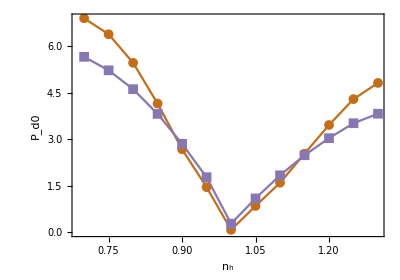

```mathematica
Pd00=ListPlot[{Pd0b32vsdensity,Pd0b16vsdensity},Frame->True,AspectRatio->0.7,BaseStyle->{FontSize->18,FontFamily->"times New Roman"},PlotStyle->{RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.528488, 0.470624, 0.701351]},(*PlotLegends->Placed[LineLegend[{"T=0.031","T=0.067"},LabelStyle->{13},LegendLayout->{"Row",1}],{0.35,0.92}],*)FrameLabel->{"n_h","P_d0"},PlotMarkers->{Automatic,10},Joined->True,FrameTicks->{{All,None},{All,None}},PlotRange->All]
```

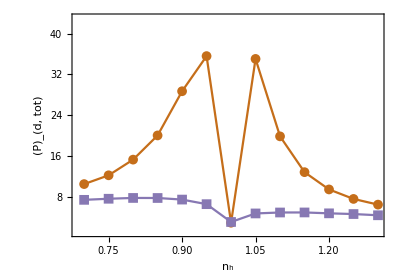

```mathematica
Pdsep2by2=ListPlot[{dcapdseptotvsn2by2b32Upp0,dcapdseptotvsn2by2b16Upp0},Frame->True,AspectRatio->0.7,BaseStyle->{FontSize->18,FontFamily->"times New Roman"},PlotStyle->{RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.528488, 0.470624, 0.701351]},(*PlotLegends->Placed[LineLegend[{"T=0.031","T=0.067"},LabelStyle->{13},LegendLayout->{"Row",1}],{0.35,0.92}],*)FrameLabel->{"n_h","(P̄)_(d, tot)"},PlotMarkers->{Automatic,10},Joined->True,PlotRange->{All,{1,43}},FrameTicks->{{All,None},{All,None}}]
```